Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

1 - 6 Calculation of gradients
Find grad f. Graph some level curves f=const. Indicate ∇f by arrows at some points of these curves.

1.  f = (x + 1) (2 y - 1)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=f[x_,y_]=(x+1) (2 y-1)
```

(1+x) (-1+2 y)

```mathematica
grad[x_,y_]=Grad[f[x,y],{x,y}]
```

{-1+2 y,2 (1+x)}

Below: the interactive plot was found in Mathematica documentation under ‘Grad’. It seems to cover what the problem description requires in terms of finding the gradient at various points. The only drawback is that it is not possible to get a gradient value for an exact, arbitrary point.

```mathematica
Manipulate[ContourPlot[f[x,y],{x,-3,3},{y,-3,3}, Epilog->Arrow[{pt,pt+grad@@pt}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-3,3},{-3,3},{-3,3}},ImageSize->Medium,ContourLabels->True,PlotLabel->Style[Framed[{{pt},{grad@@pt}}],11,Blue]],{{pt,{.01,-0.1}},Locator},FrameLabel->"Click a point to see: the point + its gradient",SaveDefinitions->True]
```

3.  f = y/x

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]=y/x
```

y/x

```mathematica
grad[x_,y_]=Grad[f[x,y],{x,y}]
```

{-y/x^2,1/x}

```mathematica
Manipulate[ContourPlot[f[x,y],{x,-8,8},{y,-100,100}, Epilog->Arrow[{pt,pt+grad@@pt}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-8,8},{-100,100},{-140,140}},ImageSize->750,ContourLabels->True,PlotLabel->Style[Framed[{{pt},{grad@@pt}}],11,Blue],FrameLabel->"Click a point to see: the point + its gradient",AspectRatio->.3],{{pt,{.01,-0.1}},Locator},SaveDefinitions->True]
```

5. f = x^4 + y^4

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]=x^4+y^4
```

x^4+y^4

```mathematica
grad[x_,y_]=Grad[f[x,y],{x,y}]
```

{4 x^3,4 y^3}

```mathematica
Manipulate[ContourPlot[f[x,y],{x,-3,3},{y,-3,3}, Epilog->Arrow[{pt,pt+grad@@pt}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-3,3},{-3,3},{-3,3}},ImageSize->400,ContourLabels->True,PlotLabel->Style[Framed[{{pt},{grad@@pt}}],11,Blue],FrameLabel->"Click a point to see: the point + its gradient",AspectRatio->.97],{{pt,{.01,-0.1}},Locator},SaveDefinitions->True]
```

7 - 10 Useful formulas for gradient and Laplacian
Prove and illustrate by an example.

7.  ∇(f^n) = n f^(n-1)∇f

9. ∇(f/g) = (1/g^2)(g∇f - g∇g)

11 - 15 Use of gradients. Electric force.
The force in an electrostatic field given by f[x, y, z] has the direction of the gradient. Find ∇f and its value at P.

11. f = xy, P: (-4, 5)

```mathematica
Clear["Global`*"]
```

```mathematica
grad[x_,y_]=Grad[x y,{x,y}]
```

{y,x}

```mathematica
grad[-4,5]
```

{5,-4}

13. f=Log[x^2+y^2], P:{8,6}

```mathematica
Clear["Global`*"]
```

```mathematica
grad[x_,y_]=Grad[Log[x^2+y^2],{x,y}]
```

{(2 x)/(x^2+y^2),(2 y)/(x^2+y^2)}

```mathematica
N[grad[8,6]]
```

{0.16,0.12}

15.  f=4 x^2+9 y^2+z^2, P:{5, -1, -1}

```mathematica
Clear["Global`*"]
```

```mathematica
grad[x_,y_,z_]=Grad[4 x^2+9 y^2+z^2,{x,y,z}]
```

{8 x,18 y,2 z}

```mathematica
grad[5,-1,-11]
```

{40,-18,-22}

18 - 23 Velocity fields
Given the velocity potential f of a flow, find the velocity v = ∇f of the field and its value v[P] at P. Sketch v[P] and the curve f = const passing through P.

19.  f=Cos[x]Cosh[y], P:(π/2,Log[2])

```mathematica
Clear["Global`*"]
```

```mathematica
velocity[x_,y_]=Grad[Cos[x] Cosh[y],{x,y}]
```

{-Cosh[y] Sin[x],Cos[x] Sinh[y]}

```mathematica
velocity[π/2,Log[2]]
```

{-5/4,0}

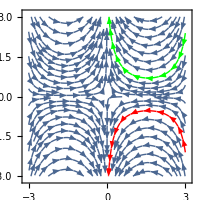

```mathematica
StreamPlot[velocity[x,y],{x,-3,3},{y,-3,3},StreamPoints->{{{{π/2,Log[2]},Green},{{0.5,-1},Red},Automatic}},ImageSize->200]
```

21.  f=ⅇ^x Cos[y], P:(1, 1/2 π)

```mathematica
Clear["Global`*"]
```

```mathematica
velocity[x_,y_]=Grad[ⅇ^x Cos[y],{x,y}]
```

{ⅇ^x Cos[y],-ⅇ^x Sin[y]}

```mathematica
velocity[1,π/2]
```

{0,-ⅇ}

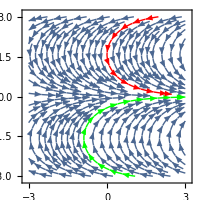

```mathematica
StreamPlot[velocity[x,y],{x,-3,3},{y,-3,3},StreamPoints->{{{{0,-ⅇ},Green},{{0,π/2},Red},Automatic}},ImageSize->200]
```

23.  At what points is the flow in problem 21 horizontal?

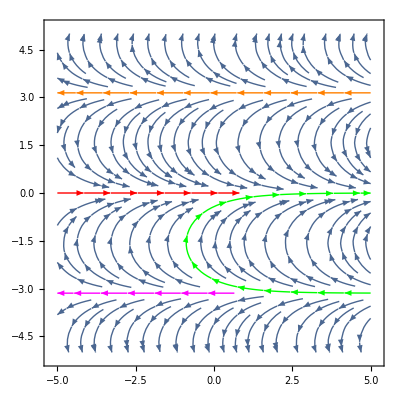

```mathematica
StreamPlot[velocity[x,y],{x,-5,5},{y,-5,5},StreamPoints->{{{{0,-ⅇ},Green},{{0,0},Red},{{0,π},Orange},{{0,-π},Magenta},Automatic}},ImageSize->400]
```

Above: The only point I found that was definitely horizontal when plotted  was (0,0). The text answer is (0,±n π), so it is a  more general formula. A couple of these identified designated points are shown above.

24 - 27 Heat flow.
Experiments show that in a temperature field, heat flows in the direction of maximum decrease of temperature T. Find this direction in general and at the given point P. Sketch that direction at P as an arrow.

25.  T=z/(x^2+y^2), P: (0, 1, 2)

```mathematica
Clear["Global`*"]
```

```mathematica
teef[x_,y_,z_]=z/(x^2+y^2)
```

z/(x^2+y^2)

```mathematica
teef[0,1,2]
```

2

```mathematica
gradT[x_,y_,z_]=Grad[-z/(x^2+y^2),{x,y,z}]
```

{(2 x z)/((x^2+y^2)^2),(2 y z)/((x^2+y^2)^2),-1/(x^2+y^2)}

```mathematica
gradT[0,1,2]
```

{0,4,-1}

```mathematica
gradT[0,3,0]
```

{0,0,-1/9}

```mathematica
{0,3,2}-%
```

{0,77/27,19/9}

The minus sign was put into the Grad expression above because I want not the maximum increase direction but the maximum decrease direction. The blue cell shows that it works with the problem point, yielding the text answer. The s.m. approached the problem of plotting by considering the isotherms at z=2, the z-plane of the problem point. I copied this approach.

```mathematica
gradX[x_,y_]={x,y,2}
```

{x,y,2}

Above: the function gradX is designed to insert the z=2 coordinate into any point pt in the interactive plot.

```mathematica
gradX[0,1]
```

{0,1,2}

```mathematica
gradb[x_,y_]=Grad[-2/(x^2+y^2), {x,y}]
```

{(4 x)/((x^2+y^2)^2),(4 y)/((x^2+y^2)^2)}

Above: the function gradb is designed to mimic gradT in 2 dimensions. It reproduces the direction of the gradient produced by gradT projected onto the z=2 plane parallel to the xy-plane.

```mathematica
gradb[0,1]
```

{0,4}

Above: testing gradb on the problem point.

```mathematica
f[x_,y_]=-2/(x^2+y^2)
```

-2/(x^2+y^2)

```mathematica
f[1,1]
```

-1

```mathematica
Manipulate[ContourPlot[f[x,y],{x,-4,4},{y,-4,4}, Epilog->{Arrow[{pt,pt+gradb@@pt}],Green,PointSize[Medium],Point[{0,1}]},PerformanceGoal->"Quality",Contours->20,PlotRange->{{-4,4},{-4,4},{-4,4}},ImageSize->400,Contours->5,ContourLabels->True,PlotLabel->Style[Framed[{{gradX@@pt},{gradT@@gradX@@pt}}],11,Blue],FrameLabel->"Temp field, showing xyz-gradient for z=2 (with problem point Green)",AspectRatio->.97],{{pt,{.01,-0.1}},Locator},SaveDefinitions->True]
```

```mathematica
pointt={1,1,-1}
```

{1,1,-1}

```mathematica
grad22[x_,y_]=Grad[-2/(x^2+y^2),{x,y}]
```

{(4 x)/((x^2+y^2)^2),(4 y)/((x^2+y^2)^2)}

```mathematica
grad22[0,3]
```

{0,4/27}

```mathematica
Show[{Plot3D[-2/(x^2+y^2),{x,-4.5,4.5},{y,-4.5,4.5},ImageSize->300,PlotRange->{-4,4},AxesLabel->{x,y,z}],Graphics3D[{PointSize[Large],Red, Point[{0,3,0}],Black,Arrow[Tube[{{0,3,0},{0,77/27,5}},.03]]}]}]
```

-Graphics3D-

```mathematica
Arrow[Tube[{{0,0,-4},{0,0,4}},.01]]
```

Below: some failed experiments trying to get the problem to show up in three dimensions. The ListPointPlot3D try does show how to make and use some tables as input to a plot.

```mathematica
data1=Flatten[Table[{(2 x z)/((x^2+y^2)^2),(2 y z)/((x^2+y^2)^2),-1/(x^2+y^2)},{x,-3,-0.1,0.5},{y,-3,3,0.5},{z,-3,3,.5}],1];
data2=Flatten[Table[{(2 x z)/((x^2+y^2)^2),(2 y z)/((x^2+y^2)^2),-1/(x^2+y^2)},{x,.1,3,0.5},{y,-3,3,0.5},{z,-3,3,.5}],1];
data3=Flatten[Table[{(2 x z)/((x^2+y^2)^2),(2 y z)/((x^2+y^2)^2),-1/(x^2+y^2)},{x,-3,3,0.5},{y,-3,-.1,0.5},{z,-3,3,.5}],1];
data4=Flatten[Table[{(2 x z)/((x^2+y^2)^2),(2 y z)/((x^2+y^2)^2),-1/(x^2+y^2)},{x,-3,3,0.5},{y,.1,3,0.5},{z,-3,3,.5}],1];
```

```mathematica
dataall=Union[data1,data2,data3,data4];
```

```mathematica
ListPointPlot3D[dataall,DataRange->{{0,10},{0,10}},PlotRange->{-30,30}]
```

-Graphics3D-

```mathematica
ContourPlot3D[-z/(x^2+y^2),{x,-.5,1.5},{y,.2,3},{z,-400,400}]
```

-Graphics3D-

```mathematica
ContourPlot3D[-z/(x^2+y^2),{x,-.5,1.5},{y,.2,3},{z,-400,400}]
```

27.  CAS project. Isotherms. Graph some curves of constant temperature (“isotherms”) and indicate directions of heat flow by arrows when the temperature equals (a) x^3 - 3xy^2, (b) Sin[x] Sinh[y], and (c) ⅇ^x Cos[y].

```mathematica
Clear["Global`*"]
```

```mathematica
grad[x_,y_]=Grad[x^3-3 x y^2,{x,y}]
```

{3 x^2-3 y^2,-6 x y}

```mathematica
Manipulate[ContourPlot[x^3-3 x y^2,{x,-2,2},{y,-2,2}, Epilog->Arrow[{pt,pt+grad@@pt}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-2,2},{-2,2},{-3,3}},ImageSize->Medium,ContourLabels->Automatic,PlotLabel->Style[Framed[{{pt},{grad@@pt}}],11,Blue]],{{pt,{.01,-0.1}},Locator},FrameLabel->"Click a point to see: the point + its gradient",SaveDefinitions->True]
```

```mathematica
Plot3D[x^3-3 x y^2,{x,-2,2},{y,-2,2},ImageSize->300]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
```

```mathematica
grad[x_,y_]=Grad[Sin[x] Sinh[y],{x,y}]
```

{Cos[x] Sinh[y],Cosh[y] Sin[x]}

```mathematica
Manipulate[ContourPlot[Sin[x] Sinh[y],{x,-2,2},{y,-2,2}, Epilog->Arrow[{pt,pt+grad@@pt}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-2,2},{-2,2},{-3,3}},ImageSize->Medium,ContourLabels->Automatic,PlotLabel->Style[Framed[{{pt},{grad@@pt}}],11,Blue]],{{pt,{.01,-0.1}},Locator},FrameLabel->"Click a point to see: the point + its gradient",SaveDefinitions->True]
```

```mathematica
Plot3D[Sin[x] Sinh[y],{x,-2,2},{y,-2,2},ImageSize->300]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
```

```mathematica
grad[x_,y_]=Grad[ⅇ^x Cos[y],{x,y}]
```

{ⅇ^x Cos[y],-ⅇ^x Sin[y]}

```mathematica
Manipulate[ContourPlot[ⅇ^x Cos[y],{x,-2,2},{y,-2,2}, Epilog->Arrow[{pt,pt+grad@@pt}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-2,2},{-2,2},{-3,3}},ImageSize->Medium,ContourLabels->Automatic,PlotLabel->Style[Framed[{{pt},{grad@@pt}}],11,Blue]],{{pt,{.01,-0.1}},Locator},FrameLabel->"Click a point to see: the point + its gradient",SaveDefinitions->True]
```

```mathematica
Show[Plot3D[{{ⅇ^x Cos[y]},{(1+x)/ⅇ+Cos[1]/ⅇ+(1+y) Cos[1]}},{x,-2,2},{y,-2,2},ImageSize->300,AxesLabel->{x,y,"z"},BoxRatios->Automatic],Graphics3D[{PointSize[Large],Green, Point[{-1,-1,ⅇ^-1 Cos[-1]}],Black,Arrowheads[{{.02,1}}],Arrow[Tube[{{-1,-1,ⅇ^-1 Cos[-1]},{1/ⅇ-1,Cos[1]-1,-1+ⅇ^-1 Cos[-1]}},.015]]}]]
```

-Graphics3D-

According to MathWorld, the equation for a tangent plane is: z=f(x_0,y_0)+f_x(x_0,y_0) (x-x_0)+f_y(x_0,y_0) (y-y_0). At the point (-1,-1),

```mathematica
z=ⅇ^-1 Cos[-1]+ⅇ^-1(x+1)+Cos[-1] (y+1)
```

(1+x)/ⅇ+Cos[1]/ⅇ+(1+y) Cos[1]

```mathematica
gradz=Grad[z,{x,y}]
```

{1/ⅇ,Cos[1]}

As the above shows, this works.

Again, from MathWorld, the equation for a normal vector at a point x_0,y_0 on a surface z=f(x,y) is given by
	N=|f_x(x_0,y_0)
f_y(x_0,y_0)
-1|,
(the vector) where f_x and f_y are partial derivatives.

```mathematica
nN={D[(1+x)/ⅇ+Cos[1]/ⅇ+(1+y) Cos[1],{x}],D[(1+x)/ⅇ+Cos[1]/ⅇ+(1+y) Cos[1],{y}],-1}
```

{1/ⅇ,Cos[1],-1}

Adding this to the arrow starting point works now, thanks to a Stack Exchange tip on the use of BoxRatio to get the axes equalized.

*******************************************************************************************

All the problems after no. 29 were omitted from the PDF version of the text.

33. Find the normal to the ellipsoid surface 6 x^2+2 y^2+z^5=225, first in general expression, then at the point P=(5,5,5). Find the unit normal.

```mathematica
Clear["Global`*"]
```

```mathematica
e1=6 x^2+2 y^2+z^2
```

6 x^2+2 y^2+z^2

Above: It looks like the constant should be dropped, it just gums up the works.

```mathematica
e2[x_,y_,z_]=Grad[e1,{x,y,z}]
```

{12 x,4 y,2 z}

```mathematica
e3=e2[5,5,5]
```

{60,20,10}

```mathematica
e44=e2[0,0,15]
```

{0,0,30}

```mathematica
e4=Norm[e3]
```

10 √41

```mathematica
e45=Norm[e44]
```

30

```mathematica
e5=e3/e4
```

```mathematica
e51=e44/e45
```

{0,0,1}

```mathematica
Show[Plot3D[√(225-6 x^2-2 y^2)==0,{x,0,9},{y,0,9},AxesLabel->Automatic,BoxRatios->Automatic],
Graphics3D[{PointSize[Large],Red, Point[{5,5,5}],Black,Arrowheads[{{.02,1}}],Arrow[Tube[{{5,5,5},{5+6/(√41),5+2/(√41),5+1/(√41)}},.03]]}]]
```

-Graphics3D-

```mathematica
e7[x_,y_,z_]=Grad[√(225-6 x^2-2 y^2)-z,{x,y,z}]
```

{-(6 x)/(√(225-6 x^2-2 y^2)),-(2 y)/(√(225-6 x^2-2 y^2)),-1}

```mathematica
e7[5,5,5]
```

{-6,-2,-1}

```mathematica
aa=√(6/225)//N
```

0.163299

```mathematica
bb=√(2/225)//N
```

0.0942809

```mathematica
cc=√(1/225)//N
```

0.0666667

```mathematica
lgrad[u_,v_]=Grad[{.1633 Cos[u] Sin[v],.0943 Sin[u] Sin[v],.0666 Cos[v]},{u,v}]
```

{{-0.1633 Sin[u] Sin[v],0.1633 Cos[u] Cos[v]},{0.0943 Cos[u] Sin[v],0.0943 Cos[v] Sin[u]},{0,-0.0666 Sin[v]}}

```mathematica
lgrad[.2,.2]
```

{{-0.00644537,0.156855},{0.0183611,0.0183611},{0,-0.0132314}}

```mathematica
6/(√41),2/(√41),1/(√41)
```

```mathematica
√225
```

15

```mathematica
Show[ParametricPlot3D[{.1633 Cos[u] Sin[v],.0943 Sin[u] Sin[v],.0666 Cos[v]},{u,0,2 π},{v,0,π},PlotStyle->Opacity[.4],BoxRatios->Automatic],Graphics3D[{PointSize[Large],Red, Point[{(.1633)^2 5,(.0943)^2 5,(.0666)^2 5}],Black,Arrowheads[{{.02,1}}],Arrow[Tube[{{(.1633)^2 5,(.0943)^2 5,(.0666)^2 5},{(.1633)^2 6/(√41),(.0943)^2 2/(√41),(.0666)^2 1/(√41)}},.001]]}]]
```

-Graphics3D-

In the parametric form, it is hard to see the arrow angle clearly, but it might be right.